### Wprowadzenie wartosci dla ladunku wlasciwego ( "q_w" ) i przenikalnosci dielektrycznej prozni ( "ϵ_o" ).

```mathematica
ClearAll["Global`*"];
```

```mathematica
qw=0.25 ×10^-3;               (* C/kg *)
```

```mathematica
ϵo=8.85×10^-12;               (* F/m *)
```

### Wprowadzenie wzorow na sile przyciagania kulombowskiego ( "F_q" ) i sile odsrodkowa ( "F_o" ) dzialajaca na poruszajacy sie ladunek punktowy (symbol "q_o"oznacza wartosc ladunku, "m" jego mase, a "r" odleglosc od srodka kuli).

```mathematica
Fq=(q ×qo)/(4×π×ϵo×r^2);
Fo=(m×v^2)/r;
```

### Wprowadzenie wzoru opisujacego zaleznosc pomiedzy ladunkiem wlasiwym, ladunkiem i masa.

```mathematica
qo=m×qw;
```

### Wykorzystanie rownosci pomiedzy sila przyciagania kulombowskiego i odsrodkowa do obliczenia predkosci ladunku ( "v" ).

```mathematica
A=Solve[Fq==Fo,v];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

### Sporzadzenie wykresu obrazujacego zaleznosc predkosci ladunku od odleglosci od srodka kuli dla trzech roznych wartosci ladunku kuli.

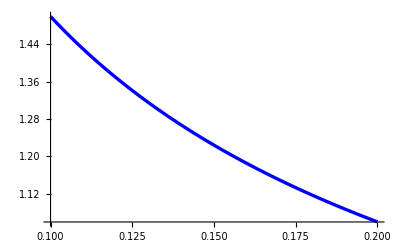

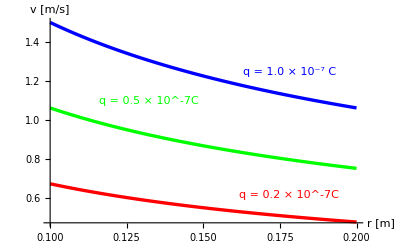

```mathematica
rys1=Plot[v/.A[[2,1]]/.q->0.2 ×10^-7,{r,0.1,0.2},
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),
DisplayFunction->Identity];
rys2=Plot[v/.A[[2,1]]/.q->0.5 ×10^-7,{r,0.1,0.2},
PlotStyle->({{RGBColor[0,1,0], Thickness[0.006]}}),
DisplayFunction->Identity];
rys3=Plot[v/.A[[2,1]]/.q->1.0 ×10^-7,{r,0.1,0.2},
PlotStyle->({{RGBColor[0,0,1], Thickness[0.006]}}),
DisplayFunction->Identity]


Show[rys1,rys2,rys3,DisplayFunction->$DisplayFunction, PlotRange->All,
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
AxesLabel->{"r [m]","v [m/s] "},
Prolog->{Text[StyleForm["q = 0.2 × 10^-7C",FontColor->RGBColor[1,0,0]],
Scaled[{0.77,0.15}]],
Text[StyleForm["q = 0.5 × 10^-7C",FontColor->RGBColor[0,1,0]],
Scaled[{0.33,0.60}]],
Text[StyleForm["q = 1.0 × 10^-7 C",FontColor->RGBColor[0,0,1]],Scaled[{0.77,0.74}]]}]
```